```mathematica
Needs["ErrorBarPlots`"]
GenerateListOfFileNames[prefix_,date_,runtimes_]:=Module[{j,fileNames},
fileNames={};
For[j=1,j≤Length[runtimes],j++,
AppendTo[fileNames,StringJoin[prefix,date,"_",ToString[runtimes[[j]]],".dat"]]
];
fileNames
];
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];


headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
```

```mathematica
DFT[list_,rev_]:=Module[{numItems,i,k,j,reconstructionCos,reconstructionSin,returnCos,errorsCos,returnSin,errorsSin,intensity},
returnCos={};
errorsCos={};
returnSin={};
errorsSin={};
reconstructionCos={};
reconstructionSin={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnCos,0];
AppendTo[returnSin,0];

];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnCos[[k+1]]=N[returnCos[[k+1]]+1/numItems*intensity*Cos[2*π *k *rev* (i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems]];,
returnCos[[k+1]]=N[returnCos[[k+1]]+2/numItems*intensity*Cos[2*π *k* rev *(i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems]];
];
];
];
(*

For[j=0,j<numItems/2,j++,
AppendTo[errorsSin,0];
AppendTo[errorsCos,0];
For[i=1,i<=numItems,i++,
intensity=list[[i]];
AppendTo[reconstructionCos,0];
AppendTo[reconstructionSin,0];
reconstructionCos[[i]]=intensity/Cos[2*π*j*rev*(i)/numItems] ;
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]=intensity/Sin[2*π*1.0001*j*rev*(i)/numItems];];
For [k=0,k<numItems/2,k++,
If[k≠j,
reconstructionCos[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(i)/numItems] )/Cos[2*π*j*rev*(i)/numItems];
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(1)/numItems] )/Sin[2*π*1.0001*j*rev*(i)/numItems]];
];
];
errorsSin[[j+1]]+=Power[reconstructionSin[[i]]-returnSin[[j+1]],2];
errorsCos[[j+1]]+=Power[reconstructionCos[[i]]-returnCos[[j+1]],2];
];
errorsSin[[j+1]]=Sqrt[errorsSin[[j+1]]/numItems];
errorsCos[[j+1]]=Sqrt[errorsCos[[j+1]]/numItems];
];
*)
{{returnSin,errorsSin},{returnCos,errorsCos}}
];
```

```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-10-20"}];
dropBoxfolder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox"}];
dataFolder=FileNameJoin[{"00School","research","testData"}];
folder=FileNameJoin[{raspberryPi}];
SetDirectory[folder];
FileNames[]
```

```mathematica
angles=Range[0,4π,2π*10/1200];
data2=Sin[angles]+9*Sin[2*angles]+10*Sin[4*angles];
```

```mathematica
data=GetFileDataset["POL2017-10-20_162159.dat"]
intensity=Normal[data[All,"COUNT"]]
ft=DFT[data2,2]
```

Dataset[<>]

{1067,1082,1044,1082,995,1016,1065,1030,1046,998,990,1070,1087,1020,1020,1042,1055,1112,964,1138,982,1068,1059,1040,1064,1027,1062,1041,1041,1051,1098,1110,1012,1075,1061,1080,1047,976,1045,1021,1012,1022,1086,1082,1098,1086,1104,1060,1004,1020,1020,1104,1071,1101,1026,1006,971,1053,1031,1006,1001,1083,1017,989,1014,1070,1031,1108,1097,1096,1108,1016,1008,996,1021,1049,1029,1049,1053,1061,1053,1099,1092,1058,1014,1088,1090,993,1089,1069,1056,995,1058,1014,1071,1005,1042,1070,994,1017,1018,1040,1059,971,1001,1044,1019,1089,1041,1032,1039,1080,1014,1101,1051,1034,1088,1120,1002,1028}

{{{0.,1.0688,9.01408,0.0459253,9.85459,-0.223491,-0.128802,-0.0942211,-0.0754463,-0.0633543,-0.0547844,-0.0483271,-0.0432498,-0.0391302,-0.0357058,-0.032804,-0.0303062,-0.0281277,-0.0262064,-0.0244957,-0.0229596,-0.0215702,-0.0203051,-0.0191463,-0.0180792,-0.0170918,-0.0161741,-0.0153175,-0.0145149,-0.0137603,-0.0130485,-0.0123749,-0.0117355,-0.011127,-0.0105464,-0.00999096,-0.00945834,-0.00894644,-0.00845339,-0.00797749,-0.00751722,-0.0070712,-0.00663816,-0.00621697,-0.00580657,-0.00540599,-0.00501435,-0.00463081,-0.0042546,-0.00388501,-0.00352134,-0.00316297,-0.00280929,-0.00245972,-0.0021137,-0.00177072,-0.00143026,-0.00109182,-0.000754905,-0.00041905,-0.0000837809,0.000251372,0.000586875,0.000923199,0.00126082,0.00160021,0.00194187,0.0022863,0.00263402,0.00298558,0.00334153,0.00370247,0.00406902,0.00444184,0.00482162,0.00520911,0.00560511,0.00601048,0.00642615,0.00685313,0.00729251,0.00774549,0.0082134,0.00869767,0.00919992,0.00972193,0.0102657,0.0108334,0.0114276,0.0120511,0.0127072,0.0133994,0.014132,0.0149099,0.0157386,0.0166248,0.0175763,0.0186021,0.0197134,0.0209233,0.0222481,0.0237077,0.0253272,0.0271381,0.0291813,0.0315105,0.034198,0.0373434,0.0410893,0.0456472,0.0513474,0.05874,0.0688258,0.0836661,0.108413,0.161292,0.404735,-0.232233,0.0888649,-0.151788,-0.035751},{}},{{-4.7011×10^-16,0.0278713,0.470444,0.00359934,1.03143,-0.0292996,-0.0203143,-0.0173887,-0.0159681,-0.0151445,-0.0146157,-0.0142523,-0.0139904,-0.0137946,-0.0136439,-0.0135253,-0.0134301,-0.0133525,-0.0132884,-0.0132347,-0.0131893,-0.0131506,-0.0131174,-0.0130886,-0.0130635,-0.0130414,-0.013022,-0.0130049,-0.0129896,-0.0129759,-0.0129637,-0.0129527,-0.0129429,-0.0129339,-0.0129258,-0.0129185,-0.0129118,-0.0129057,-0.0129002,-0.0128951,-0.0128905,-0.0128863,-0.0128825,-0.012879,-0.0128758,-0.0128729,-0.0128702,-0.0128678,-0.0128657,-0.0128637,-0.012862,-0.0128604,-0.012859,-0.0128579,-0.0128568,-0.012856,-0.0128553,-0.0128547,-0.0128543,-0.012854,-0.0128539,-0.012854,-0.0128542,-0.0128545,-0.012855,-0.0128556,-0.0128564,-0.0128573,-0.0128584,-0.0128597,-0.0128612,-0.0128628,-0.0128647,-0.0128667,-0.012869,-0.0128715,-0.0128743,-0.0128773,-0.0128807,-0.0128844,-0.0128884,-0.0128928,-0.0128976,-0.0129029,-0.0129087,-0.0129151,-0.0129221,-0.0129298,-0.0129383,-0.0129477,-0.0129581,-0.0129697,-0.0129826,-0.012997,-0.0130132,-0.0130314,-0.0130521,-0.0130756,-0.0131025,-0.0131334,-0.0131692,-0.0132111,-0.0132604,-0.013319,-0.0133894,-0.0134752,-0.0135812,-0.0137145,-0.0138858,-0.0141113,-0.0144183,-0.0148536,-0.0155069,-0.0165714,-0.0185499,-0.0232878,-0.0477029,0.0212502,-0.00580027,0.00593898,0.000466064},{}}}

```mathematica
GetLinearPolarizationFraction[fileName_]:=Module[{data,angle,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
intensity=fc[[2]][[1]];
linearPolarization=Sqrt[(fc[[2]][[3]])^2+(fc[[1]][[3]])^2];
linearPolarizationFraction=linearPolarization/intensity
];
SetAttributes[GetLinearPolarizationFraction,Listable];
GetAngle[fileName_]:=Module[{data,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
.5*ArcTan[fc[[1]][[3]],fc[[2]][[3]]]
];
SetAttributes[GetAngle,Listable];
```

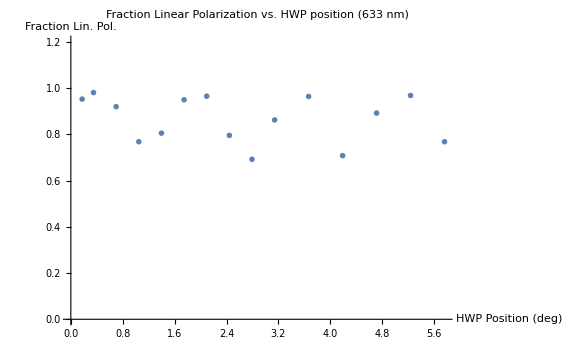

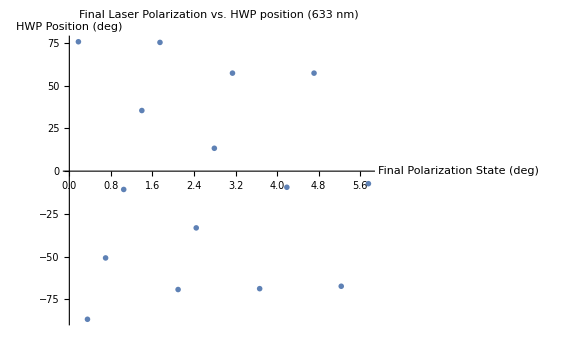

```mathematica
hwpAngles={10,20,40,60,80,100,120,140,160,180,210,240,270,300,330};
hwpAngles=hwpAngles*π/180;
percentPol={.9520,.9802,.9193,.7678,.8048,.9489,.9646,.7951,.6917,.8619,.9635,.7075,.8916,.9676,.7677};
laserPolarizationAngle={75.65,-86.60,-50.74,-10.71,35.44,75.26,-69.21,-33.17,13.37,57.30,-68.70,-9.42,57.30,-67.29,-7.32};
plotTitle="Fraction Linear Polarization vs. HWP position (633 nm)";
xAxisTitle="Fraction Lin. Pol.";
yAxisTitle="HWP Position (deg)";
plot633=ListPlot[Transpose[{hwpAngles,percentPol}],PlotMarkers->{Automatic,Medium},LabelStyle->18,ImageSize->Large,PlotRange->{0,1.2},PlotLabel-> plotTitle,AxesLabel->{yAxisTitle,xAxisTitle}]

plotTitle="Final Laser Polarization vs. HWP position (633 nm)";
yAxisTitle="Final Polarization State (deg)";
xAxisTitle="HWP Position (deg)";
ListPlot[Transpose[{hwpAngles,laserPolarizationAngle}],PlotMarkers->{Automatic,Medium},LabelStyle->18,ImageSize->Large,PlotLabel-> plotTitle,AxesLabel->{yAxisTitle,xAxisTitle}]
```

## Determing Fraction of LP without the HWP in.

```mathematica
times={101927,101951,102015,102039,102103,102127,102151,102214,102238,102302};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
{Mean[fractions],StandardDeviation[fractions]}
{Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
```

Part::partw: Part 3 of {{0.934337,0.0178053,0.838144,-0.00378385,0.0430723,0.00767121,0.0389968,0.00697104,0.0119072,0.00219782,0.00211289,0.000715998,0.00111527,0.000486652,0.000233695,0.0000656286,-0.000236043,0.000673183,0.000141572,0.000569157,0.000897631,-0.000342805,0.000694786,-0.000469646,-0.000192763},{0.168839,0.705212,2.87113,0.941421,0.874224,0.378849,«14»,0.376203,0.895423,0.929209,0.886885,0.701453}} does not exist.

Part::partw: Part 3 of {{0.,0.00952517,0.407158,-0.0189472,-0.00631099,-0.0380175,0.0131694,-0.013542,0.00761192,0.000661373,0.0022977,0.00212554,0.000761913,0.00204677,0.000686574,0.00118409,-0.000112924,-1.78654×10^-7,0.0000940706,0.000026993,0.00158061,-0.000438659,0.00197613,-0.000457101,0.000534003},{0.,143.579,167.563,46.8104,29.5425,216.962,«13»,7.43102,56.8384,6.74714,6.41946,6.04039,5.84975}} does not exist.

Part::partw: Part 3 of {{0.933909,0.0109901,0.838778,-0.00640784,0.0424918,0.00579313,0.0399577,0.00600378,0.0125881,0.000958714,0.00279805,-0.00138702,0.00101132,-0.000121469,0.000704308,0.000972929,0.000153898,0.00022097,-0.000475931,-0.000846433,-1.19203×10^-6,-0.000847843,0.000134985,-0.0000445559,0.000330239},{0.168796,0.702291,2.85288,0.899609,0.89833,«15»,0.378578,0.922513,0.89812,0.872683,0.69984}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{1}
 |  |  |  |

Part::partw: Part 3 of {{0.,0.00952517,0.407158,-0.0189472,-0.00631099,-0.0380175,0.0131694,-0.013542,0.00761192,0.000661373,0.0022977,0.00212554,0.000761913,0.00204677,0.000686574,0.00118409,-0.000112924,-1.78654×10^-7,0.0000940706,0.000026993,0.00158061,-0.000438659,0.00197613,-0.000457101,0.000534003},{0.,143.579,167.563,46.8104,29.5425,216.962,«13»,7.43102,56.8384,6.74714,6.41946,6.04039,5.84975}} does not exist.

Part::partw: Part 3 of {{0.934337,0.0178053,0.838144,-0.00378385,0.0430723,0.00767121,0.0389968,0.00697104,0.0119072,0.00219782,0.00211289,0.000715998,0.00111527,0.000486652,0.000233695,0.0000656286,-0.000236043,0.000673183,0.000141572,0.000569157,0.000897631,-0.000342805,0.000694786,-0.000469646,-0.000192763},{0.168839,0.705212,2.87113,0.941421,0.874224,0.378849,«14»,0.376203,0.895423,0.929209,0.886885,0.701453}} does not exist.

Part::partw: Part 3 of {{0.,0.00840771,0.407166,-0.0178518,-0.00704743,-0.0358731,0.0107785,-0.0143879,0.00644449,-0.000470579,0.0010666,0.000119143,0.00032001,-0.000421924,0.000644659,0.000589066,0.00113447,0.00159921,0.00054228,0.00107469,0.000105393,-0.000133985,-0.000844729,-0.000612704,-0.000291777},{0.,137.559,169.877,45.1509,28.7135,227.123,«13»,7.18706,59.0872,6.55554,6.28363,5.88089,5.6814}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{28.6479 ArcTan[{{0.,0.00952517,0.407158,-0.0189472,-0.00631099,-0.0380175,0.0131694,-0.013542,0.00761192,0.000661373,0.0022977,0.00212554,0.000761913,0.00204677,0.000686574,0.00118409,-0.000112924,-1.78654×10^-7,0.0000940706,0.000026993,0.00158061,-0.000438659,0.00197613,-0.000457101,0.000534003},{0.,143.579,167.563,46.8104,29.5425,216.962,19.0624,20.863,16.1735,15.4279,114.126,12.5566,11.4999,10.6386,9.9291,75.6923,8.7032,8.26238,7.81295,7.43102,56.8384,6.74714,6.41946,6.04039,5.84975}}⟦3⟧,{{0.934337,0.0178053,0.838144,-0.00378385,0.0430723,0.00767121,0.0389968,0.00697104,0.0119072,0.00219782,0.00211289,0.000715998,0.00111527,0.000486652,0.000233695,0.0000656286,-0.000236043,0.000673183,0.000141572,0.000569157,0.000897631,-0.000342805,0.000694786,-0.000469646,-0.000192763},{0.168839,0.705212,2.87113,0.941421,0.874224,0.378849,0.944374,0.82567,0.732921,0.852342,0.378941,0.826574,0.840618,0.840042,0.828975,0.378993,0.851941,0.744052,0.825851,0.903798,0.376203,0.895423,0.929209,0.886885,0.701453}}⟦3⟧],28.6479 ArcTan[{{0.,0.00840771,0.407166,-0.0178518,-0.00704743,-0.0358731,0.0107785,-0.0143879,0.00644449,-0.000470579,0.0010666,0.000119143,0.00032001,-0.000421924,0.000644659,0.000589066,0.00113447,0.00159921,0.00054228,0.00107469,0.000105393,-0.000133985,-0.000844729,-0.000612704,-0.000291777},{0.,137.559,169.877,45.1509,28.7135,227.123,18.4908,20.3219,15.7162,15.0138,118.878,12.2341,11.2023,10.4221,9.64159,78.7605,8.4176,7.99087,7.61095,7.18706,59.0872,6.55554,6.28363,5.88089,5.6814}}⟦3⟧,{{0.933909,0.0109901,0.838778,-0.00640784,0.0424918,0.00579313,0.0399577,0.00600378,0.0125881,0.000958714,0.00279805,-0.00138702,0.00101132,-0.000121469,0.000704308,0.000972929,0.000153898,0.00022097,-0.000475931,-0.000846433,-1.19203×10^-6,-0.000847843,0.000134985,-0.0000445559,0.000330239},{0.168796,0.702291,2.85288,0.899609,0.89833,0.381508,0.927487,0.82599,0.741492,0.854463,0.37521,0.832713,0.85479,0.854185,0.835246,0.375218,0.859539,0.751013,0.82706,0.893633,0.378578,0.922513,0.89812,0.872683,0.69984}}⟦3⟧],28.6479 ArcTan[{{0.,0.00673194,0.404105,-0.0234107,-0.00727477,-0.0407152,0.012456,-0.0150651,0.00761122,-0.00147675,0.00219314,-0.000602026,0.00144657,-0.00105106,0.00139249,-0.000583826,0.000540114,0.0000701744,-0.000170014,-0.000246941,-0.000795438,-0.00108327,-0.000525163,-0.000616488,0.0000726109},{0.,133.253,170.698,43.8054,27.3374,221.025,17.4726,19.7364,14.992,14.5797,116.662,11.8336,10.7214,10.0424,9.26685,77.0363,8.12859,7.74766,7.34174,6.96017,57.8892,6.32996,6.02727,5.66506,5.46037}}⟦3⟧,{{0.928359,0.0136942,0.832508,-0.00562442,0.0429036,0.00796958,0.040335,0.00886725,0.0125213,0.00380965,0.00222287,0.000273248,0.000786947,0.000093,-0.000159698,0.00153816,-0.000706235,0.00179647,-0.00086587,0.000767732,0.0000791508,0.00010765,0.000818332,0.000992403,0.000275203},{0.168068,0.699553,2.84163,0.903099,0.901613,0.380002,0.919965,0.812007,0.7312,0.839804,0.374814,0.831387,0.86792,0.865098,0.836882,0.374706,0.841994,0.742383,0.810264,0.881982,0.376113,0.926723,0.896614,0.876653,0.697398}}⟦3⟧],28.6479 ArcTan[{{0.,0.00760558,0.403964,-0.0190622,-0.00763444,-0.0364483,0.00857499,-0.0146442,0.00443407,-0.00101902,0.000754828,-0.000410758,0.000223218,0.000260393,0.0000199224,0.000294454,0.000521054,-0.000380092,-8.47454×10^-6,0.000143374,0.000129411,-0.000349636,-0.000311094,-0.000352046,-0.000475201},{0.,131.581,171.365,42.9549,27.3417,225.683,17.6751,19.3016,14.9496,14.2381,118.279,11.6247,10.5811,9.81493,9.1289,78.576,7.96069,7.57643,7.19937,6.80892,58.8575,6.20409,5.96713,5.55167,5.37387}}⟦3⟧,{{0.925638,0.0147667,0.829436,-0.00410676,0.0388395,0.00656062,0.036379,0.00666009,0.0115566,0.00175501,0.00261772,0.000181967,0.000974256,-0.000203374,0.000707326,-0.0012908,0.000334687,-0.000913954,-0.000095907,-0.00101934,0.000282777,-0.000994036,-0.000964471,-0.000127263,0.000029726},{0.166703,0.693183,2.83534,0.899772,0.879737,0.375985,0.896236,0.824487,0.742336,0.855317,0.37316,0.825719,0.842131,0.84184,0.825841,0.373154,0.857499,0.749248,0.82435,0.87029,0.373415,0.905279,0.895071,0.867574,0.691163}}⟦3⟧],28.6479 ArcTan[{{0.,0.00741479,0.403873,-0.0220762,-0.00877704,-0.0395,0.0116124,-0.0136742,0.00679309,-0.00014359,0.00229019,0.000917084,0.000838634,0.00121972,0.00017884,0.00126555,0.00112457,0.000584015,2.01565×10^-6,0.000486609,-0.0000692477,-0.000154534,0.000632695,-0.000205769,0.0000338236},{0.,137.894,168.812,45.2871,28.7044,219.826,18.4545,20.1679,15.6997,14.8855,115.854,12.1534,11.0746,10.3077,9.53363,76.7704,8.32155,7.97208,7.56706,7.18706,57.5636,6.53835,6.2464,5.85376,5.66637}}⟦3⟧,{{0.930887,0.0141832,0.834456,-0.00533624,0.0417741,0.00713493,0.0381832,0.00600737,0.0109629,0.000279956,0.00262241,-0.000565996,0.00198875,0.000258869,0.00262574,0.000232548,0.00168939,0.0004146,-0.0000812519,0.000871042,0.000922466,0.000452713,-0.000318984,0.000562986,-0.00058441},{0.167932,0.700801,2.84083,0.929649,0.878172,0.375868,0.89059,0.81298,0.749004,0.840041,0.377684,0.839627,0.856179,0.855044,0.84024,0.377694,0.845113,0.759232,0.812702,0.854364,0.372789,0.907499,0.921283,0.873959,0.698397}}⟦3⟧],28.6479 ArcTan[{{0.,0.00656878,0.403392,-0.0216229,-0.00868922,-0.0393701,0.0106491,-0.0158452,0.00811341,-0.000759638,0.00294073,-0.000481209,0.00099057,-0.00025609,0.000478552,-0.000251417,0.000818837,-0.000352976,-0.0001086,-0.000192954,0.000501199,-0.000471843,0.000914529,-0.000184327,0.0000607516},{0.,134.514,170.313,44.6403,28.2222,218.389,18.1589,20.2834,15.3982,14.8864,115.069,12.1306,11.0689,10.2965,9.54084,76.0183,8.32521,7.95785,7.51727,7.13892,57.1996,6.49,6.20369,5.80327,5.61739}}⟦3⟧,{{0.931372,0.00663243,0.837741,-0.00801172,0.0439574,0.00671246,0.0407913,0.00831901,0.0129851,0.00204034,0.00193431,-0.00072475,0.000226035,0.000209251,0.000370582,0.000929762,0.0000795855,0.00108149,0.0000550555,0.000134452,0.000835107,-0.000219707,-0.00027053,-0.000255192,-0.0000191835},{0.168762,0.695844,2.8384,0.930154,0.893747,0.380678,0.922972,0.831315,0.740031,0.844352,0.378845,0.833416,0.85366,0.852,0.835329,0.378793,0.847899,0.752194,0.830272,0.889946,0.377008,0.923488,0.920494,0.876473,0.694054}}⟦3⟧],28.6479 ArcTan[{{0.,0.00704138,0.406532,-0.022654,-0.00581252,-0.0398549,0.0118832,-0.0127974,0.00700794,0.000268909,0.00245463,-0.000225702,0.00203336,-0.000188476,0.00155472,0.000184782,0.000231406,0.000672724,0.000558701,0.000946939,-0.0000239772,0.000167398,-0.000688321,0.0000505827,-0.000138052},{0.,134.913,169.637,44.5198,28.0066,218.614,17.8748,19.8602,15.1884,14.5932,115.657,11.9597,10.8514,10.1546,9.4151,76.4045,8.25106,7.8237,7.43953,7.03239,57.173,6.40888,6.16099,5.7373,5.55305}}⟦3⟧,{{0.928572,0.0130484,0.831576,-0.00456028,0.0406778,0.00943944,0.0397202,0.00835427,0.0137234,0.000866907,0.00316214,-0.00075619,0.000935279,-0.0000263723,-0.000634603,0.000495797,-0.000526451,0.000684418,-0.00107209,0.000320059,-0.00156222,0.000147318,-0.00126388,0.00046962,-0.000183823},{0.167877,0.69814,2.84622,0.892646,0.893181,0.379339,0.919764,0.815384,0.731252,0.86344,0.375081,0.82821,0.88221,0.879172,0.834311,0.37504,0.86456,0.741457,0.816955,0.881902,0.376436,0.913421,0.890187,0.86967,0.696098}}⟦3⟧],28.6479 ArcTan[{{0.,0.00810155,0.404734,-0.0189982,-0.0077382,-0.0372591,0.00960138,-0.015466,0.00714428,-0.00109408,0.00206933,-0.000583956,0.000109589,-0.00108666,-0.000202413,-0.000368049,0.00046674,-0.0000420849,0.000196468,0.000446845,0.00105422,0.00118262,0.00128588,0.000806196,0.000190126},{0.,130.49,171.512,42.9182,27.3762,221.85,17.6108,19.4438,14.9468,14.3125,116.184,11.6918,10.7108,9.95484,9.19507,77.029,8.01038,7.64587,7.25432,6.88338,57.899,6.25599,5.97905,5.59302,5.40687}}⟦3⟧,{{0.927965,0.00973821,0.832866,-0.0072301,0.0402365,0.00601072,0.0380538,0.00620764,0.0110409,0.00107381,0.000668292,-0.000503774,-0.00022987,0.000493647,0.000845814,0.000624036,0.000563817,0.00034201,-0.000459175,0.000734838,-0.0000484123,0.000746553,-0.000193405,0.000472765,0.000205427},{0.16754,0.695471,2.83368,0.934996,0.868917,0.377465,0.914662,0.828248,0.738908,0.849091,0.376392,0.834269,0.836039,0.835477,0.833504,0.376383,0.850909,0.749713,0.828647,0.885191,0.374076,0.895242,0.92704,0.863437,0.692854}}⟦3⟧],28.6479 ArcTan[{{0.,0.00909782,0.402919,-0.0189572,-0.00661159,-0.0384081,0.0121552,-0.0141901,0.00640913,-0.000398256,0.00144038,0.00028174,0.000357664,0.000209853,0.00109463,0.000422205,0.00042788,0.000895954,0.000489145,0.00055133,0.000617349,-0.000597946,0.000610159,3.2767×10^-8,0.000361375},{0.,136.013,168.831,44.3526,27.9871,220.347,18.0471,19.924,15.3968,14.6963,115.592,11.9753,10.9593,10.1519,9.42037,76.7843,8.25148,7.82605,7.42102,7.05033,57.6124,6.42664,6.11774,5.752,5.55622}}⟦3⟧,{{0.925498,0.0158524,0.829902,-0.00480944,0.0417123,0.00694295,0.0379511,0.00739208,0.0113793,0.00197113,0.00116132,-0.00022896,0.000489619,-0.000254221,0.000137141,0.000149825,-0.000227962,0.000395289,0.0000775152,0.000224841,0.000185183,0.00014961,0.000643196,0.000771682,-0.0000829825},{0.167022,0.699418,2.83677,0.91327,0.882006,0.377279,0.925396,0.81464,0.721395,0.84395,0.372336,0.824646,0.834541,0.834066,0.828934,0.372356,0.845811,0.73063,0.815304,0.888003,0.374173,0.904324,0.905552,0.875137,0.696142}}⟦3⟧],28.6479 ArcTan[{{0.,0.00763041,0.403872,-0.0200592,-0.00638055,-0.0374692,0.0107971,-0.0140632,0.00622729,0.00136753,0.00119788,0.00128953,0.00098877,-0.000580179,0.00077264,-0.0000456786,-0.0000891244,0.000372914,-0.0000857374,0.00111615,0.000620041,0.00226024,-0.000173681,0.00173521,-0.00033002},{0.,133.827,169.076,44.2917,27.8723,215.453,17.9575,19.9244,15.3412,14.6113,113.298,11.9379,10.9103,10.2053,9.4287,75.0333,8.23978,7.83889,7.40878,7.05693,56.3402,6.40577,6.16478,5.72956,5.55526}}⟦3⟧,{{0.925122,0.00934604,0.831089,-0.00620385,0.0425657,0.00772307,0.0399911,0.00747825,0.0125052,0.00196133,0.00267041,-0.000137192,0.00112887,0.000519284,0.00032413,0.000294851,0.000714744,0.000205102,0.00109431,0.0010447,0.0000897146,0.000671345,-0.00112577,-0.000275006,0.00021743},{0.167495,0.69439,2.83384,0.905575,0.893292,0.377206,0.912989,0.825113,0.732311,0.860297,0.37532,0.809157,0.859571,0.85779,0.812123,0.375294,0.860302,0.74176,0.825289,0.879081,0.37432,0.915565,0.904587,0.868174,0.692225}}⟦3⟧]}

{{1/10 (1.08094 √(({{0.,0.00763041,0.403872,-0.0200592,-0.00638055,-0.0374692,0.0107971,11,-0.0000857374,0.00111615,0.000620041,0.00226024,-0.000173681,0.00173521,-0.00033002},1}⟦3⟧)^2+({{0.925122,0.00934604,0.831089,19,-0.00112577,-0.000275006,0.00021743},1}⟦3⟧)^2)+1.0805 √(({1}⟦3⟧)^2+1^2)+6+1.07077 1+1.07028 √(({{0.,23,0.000534003},{1}}⟦3⟧)^2+({{1},{1}}⟦3⟧)^2)),23,1/10 (1)},{1}}
 |  |  |  |

{1/10 (28.6479 ArcTan[{{0.,0.00656878,0.403392,-0.0216229,-0.00868922,-0.0393701,0.0106491,-0.0158452,0.00811341,-0.000759638,0.00294073,-0.000481209,0.00099057,-0.00025609,0.000478552,-0.000251417,0.000818837,-0.000352976,-0.0001086,-0.000192954,0.000501199,-0.000471843,0.000914529,-0.000184327,0.0000607516},{0.,134.514,170.313,19,6.20369,5.80327,5.61739}}⟦3⟧,1]+9),1/3 √1}
 |  |  |  |

-Graphics-

-Graphics-

## Increasing motor delay to 5 ms

{121232,121302,121328,121355,121421,121448,121514,121541,121607,121633}

{0.993895,0.999145,0.996628,1.00013,0.996001,0.999871,0.997476,0.998485,0.996484,0.998307}

{32.0171,32.034,32.0559,31.9752,32.0781,32.1003,32.1357,32.0703,32.0609,32.0655}

{0.997642,0.00193431}

{32.0593,0.0441424}

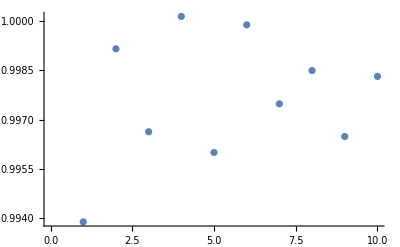

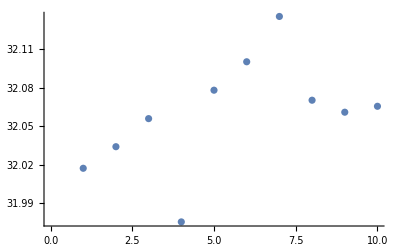

```mathematica
times={121232,121302,121328,121355,121421,121448,121514,121541,121607,121633}
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
{Mean[fractions],StandardDeviation[fractions]}
{Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
```

### Decreasing motor delay to 2.5 ms, as it didn’t seem to make a difference. HWP is now in and at 0 degrees. Stepping through in 20 degree increments.

```mathematica
hwpAngles=Range[0,360,20];
hwpResults=hwpAngles
```

{0,20,40,60,80,100,120,140,160,180,200,220,240,260,280,300,320,340,360}

#### HWP=0

{123902,123926,123949,124013,124037}

{0.117769,0.117214,0.116313,0.118792,0.118036}

{89.8255,89.5994,89.8399,89.4796,89.8961}

{0.117625,0.000927877}

{89.7281,0.179263}

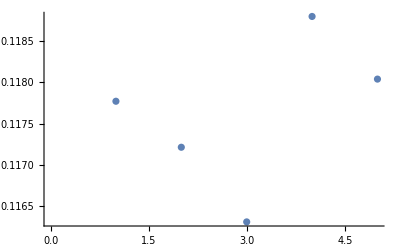

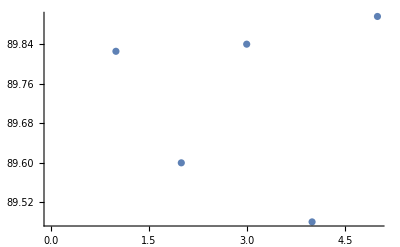

```mathematica
times={123902,123926,123949,124013,124037}
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[1]]={hwpAngles[[1]],polFraction,laserAngle};
```

#### HWP=20

{124408,124432,124456,124520,124544}

{0.561126,0.560293,0.55734,0.559659,0.561003}

{0.371483,0.378377,0.257209,0.126633,0.39299}

{0.559884,0.00153988}

{0.305339,0.113627}

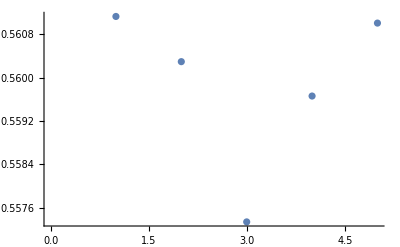

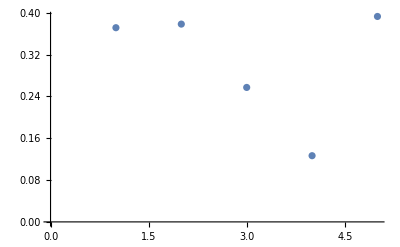

```mathematica
times={124408,124432,124456,124520,124544}
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[2]]={hwpAngles[[2]],polFraction,laserAngle};
```

#### HWP=40

{24.0238,24.0191,24.1169,24.054,24.0129}

{0.954096,0.00167881}

{24.0453,0.0429996}

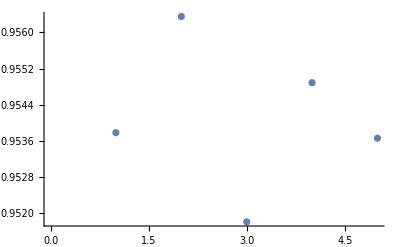

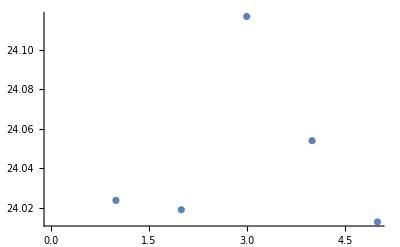

```mathematica
times={124824,124849,124913,124937,125001};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[3]]={hwpAngles[[3]],polFraction,laserAngle};
```

#### HWP=60

{0.914525,0.915684,0.912582,0.913423,0.915036}

{45.7607,45.9271,45.6936,45.8244,45.7357}

{0.91425,0.00124659}

{45.7883,0.0909161}

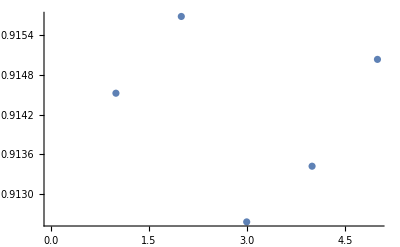

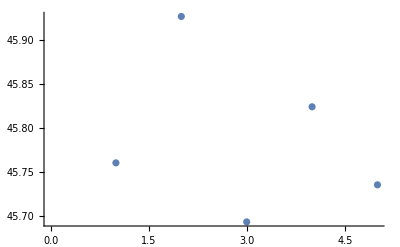

```mathematica
times={125313,125337,125401,125425,125448};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[4]]={hwpAngles[[4]],polFraction,laserAngle};
```

#### HWP = 80

{0.428582,0.430911,0.42928,0.430998,0.427847}

{70.9689,71.0549,71.094,71.1311,71.0526}

{0.429523,0.00140155}

{71.0603,0.0603946}

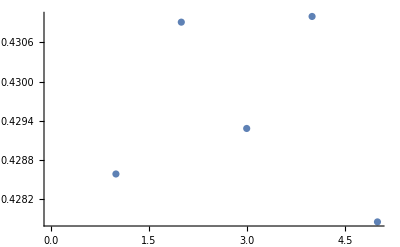

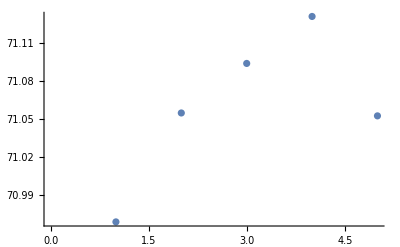

```mathematica
times={125741,125804,125828,125852,125916};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[5]]={hwpAngles[[5]],polFraction,laserAngle};
```

#### HWP = 100

{0.266606,0.271295,0.267216,0.268309,0.270276}

{-19.4409,-19.3269,-19.2605,-19.369,-19.2328}

{0.26874,0.00199662}

{-19.326,0.0837018}

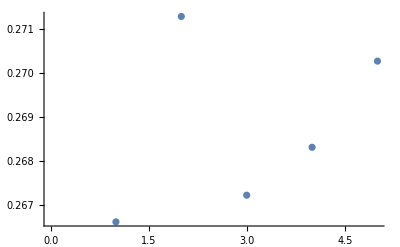

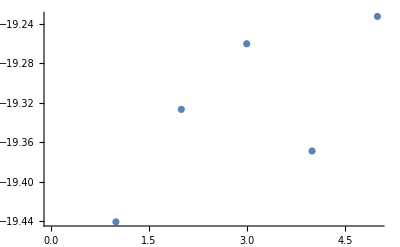

```mathematica
times={132036,132100,132124,132148,132212};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[6]]={hwpAngles[[6]],polFraction,laserAngle};
```

#### HWP = 120

{0.778338,0.781365,0.78146,0.780442,0.780903}

{11.2568,11.1569,11.1808,11.2376,11.188}

{0.780502,0.00127557}

{11.204,0.041633}

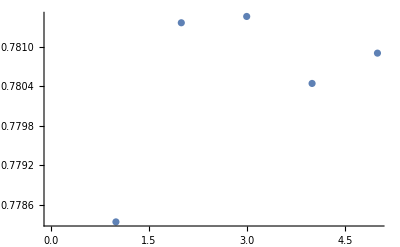

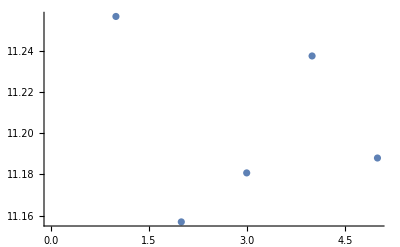

```mathematica
times={132626,132651,132715,132739,132803};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[7]]={hwpAngles[[7]],polFraction,laserAngle};
```

#### HWP = 140

{1.0009,0.997439,0.998875,0.996983,1.00011}

{33.2202,33.1506,33.1781,33.1609,33.173}

{0.99886,0.00167695}

{33.1765,0.0266393}

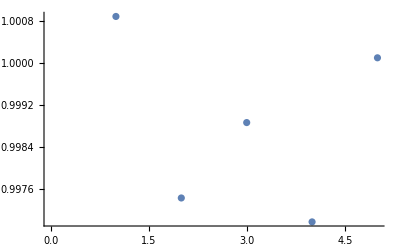

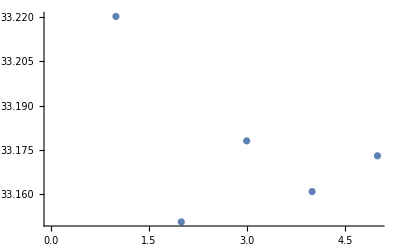

```mathematica
times={133050,133114,133138,133202,133225};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[8]]={hwpAngles[[8]],polFraction,laserAngle};
```

#### On the previous run, I note the high linear polarization and the closeness, to the angle measured without the HWP in.

#### HWP = 160

{0.726323,0.728362,0.725786,0.726653,0.729184}

{54.4768,54.4603,54.512,54.3472,54.4857}

{0.727262,0.00144362}

{54.4564,0.0638721}

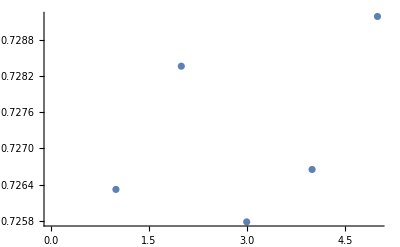

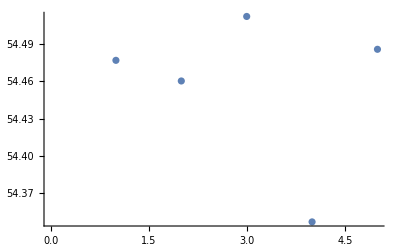

```mathematica
times={133757,133821,133845,133909,133933};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[9]]={hwpAngles[[9]],polFraction,laserAngle};
```

#### HWP = 180

{0.126038,0.122972,0.124888,0.122073,0.12316}

{-84.1457,-84.4907,-83.8436,-83.7251,-84.2006}

{0.123826,0.00160194}

{-84.0812,0.303871}

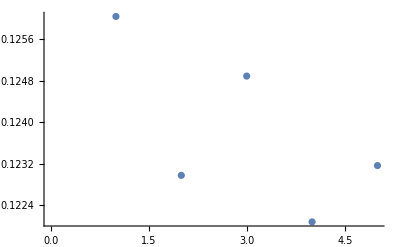

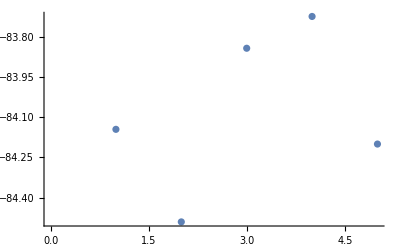

```mathematica
times={134151,134215,134239,134303,134327};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[10]]={hwpAngles[[10]],polFraction,laserAngle};
```

```mathematica
hwpResults=Take[hwpResults,{1,10}]
```

{{0,{0.117625,0.000927877},{89.7281,0.179263}},{20,{0.559884,0.00153988},{0.305339,0.113627}},{40,{0.954096,0.00167881},{24.0453,0.0429996}},{60,{0.91425,0.00124659},{45.7883,0.0909161}},{80,{0.429523,0.00140155},{71.0603,0.0603946}},{100,{0.26874,0.00199662},{-19.326,0.0837018}},{120,{0.780502,0.00127557},{11.204,0.041633}},{140,{0.99886,0.00167695},{33.1765,0.0266393}},{160,{0.727262,0.00144362},{54.4564,0.0638721}},{180,{0.123826,0.00160194},{-84.0812,0.303871}}}

```mathematica
Transpose[hwpResults]
```

{{0,20,40,60,80,100,120,140,160,180},{{0.117625,0.000927877},{0.559884,0.00153988},{0.954096,0.00167881},{0.91425,0.00124659},{0.429523,0.00140155},{0.26874,0.00199662},{0.780502,0.00127557},{0.99886,0.00167695},{0.727262,0.00144362},{0.123826,0.00160194}},{{89.7281,0.179263},{0.305339,0.113627},{24.0453,0.0429996},{45.7883,0.0909161},{71.0603,0.0603946},{-19.326,0.0837018},{11.204,0.041633},{33.1765,0.0266393},{54.4564,0.0638721},{-84.0812,0.303871}}}

```mathematica
newList={};
Length[hwpResults]
For[j=1,j≤Length[hwpResults],j++,
AppendTo[newList,{{hwpResults[[j]][[1]]*π/180,hwpResults[[j]][[2]][[1]]},ErrorBar[hwpResults[[j]][[2]][[2]]]}];
];
newList2={};
For[j=1,j≤Length[hwpResults],j++,
AppendTo[newList2,{{hwpResults[[j]][[1]]*π/180,hwpResults[[j]][[3]][[1]]},ErrorBar[hwpResults[[j]][[3]][[2]]]}];
];
plotTitle="Fraction Linear Polarization vs. HWP position (795 nm)";
xAxisTitle="Fraction of Linear Polarization";
yAxisTitle="HWP Position (deg)";
plot795=ErrorListPlot[newList,PlotMarkers->{Automatic,Medium},LabelStyle->18,ImageSize->Large,PlotRange->{0,1},PlotLabel-> plotTitle,AxesLabel->{yAxisTitle,xAxisTitle}]
plotTitle="Final Laser Polarization vs. HWP position (795 nm)";
yAxisTitle="Final Polarization State (deg)";
xAxisTitle="HWP Position (deg)";
plottingOptions={PlotMarkers->{Automatic,Medium},LabelStyle->18,ImageSize->Large,PlotLabel-> plotTitle,AxesLabel->{yAxisTitle,xAxisTitle}};
ErrorListPlot[newList2,Evaluate[plottingOptions]]
```

0

ErrorListPlot[{},PlotMarkers→{Automatic,Medium},LabelStyle→18,ImageSize→Large,PlotRange→{0,1},PlotLabel→Fraction Linear Polarization vs. HWP position (795 nm),AxesLabel→{HWP Position (deg),Fraction of Linear Polarization}]

ErrorListPlot[{},{PlotMarkers→{Automatic,Medium},LabelStyle→18,ImageSize→Large,PlotLabel→Final Laser Polarization vs. HWP position (795 nm),AxesLabel→{Final Polarization State (deg),HWP Position (deg)}}]

```mathematica
retardance633=780^2/(2 633);
N[retardance633/633]

retardance795=780^2/(2 795);
N[retardance795/795]
```

0.759192

0.48131

#### According to a Chp 22 in an optics handbook (chapter authored by Russell A. Chipman), We have the following mueller matrix for a general retarder

```mathematica
LR[θfast_,retardance_]:=({{1, 0, 0, 0}, {0, Cos[2θfast]^2+Sin[2θfast]^2Cos[2π retardance], Sin[2θfast]Cos[2θfast](1-Cos[2π retardance]), -Sin[2θfast]Sin[2π retardance]}, {0, Sin[2θfast]Cos[2θfast](1-Cos[2π retardance]), Sin[2θfast]^2+Cos[2θfast]Cos[2π retardance]^2, Cos[2 θfast]Sin[2π retardance]}, {0, Sin[2θfast]Sin[2π retardance], -Cos[2 θfast]Sin[2π retardance], Cos[2π retardance]}})
LRzero[δ_]:=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[δ], Sin[δ]}, {0, 0, -Sin[δ], Cos[δ]}});
LPzero=1/2({{1, 1, 0, 0}, {1, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

#### We will assume our incident vector was 100% linearly polarized in the horizontal direction

```mathematica
inc=({{1}, {1}, {0}, {0}})
MatrixForm[(MuellerRotation[θ].LRzero[δ].Transpose[MuellerRotation[θ]])]
```

{{1},{1},{0},{0}}

MuellerRotation[θ].{{1,0,0,0},{0,1,0,0},{0,0,{0.569006,0.886579,0.890933,0.999685},{0.822334,0.462577,0.454134,0.0250974}},{0,0,{-0.822334,-0.462577,-0.454134,-0.0250974},{0.569006,0.886579,0.890933,0.999685}}}.Transpose[MuellerRotation[θ]]

#### A useful tool is the rotation matrix

```mathematica
MuellerRotation[θ_]:=({{1, 0, 0, 0}, {0, Cos[2θ], -Sin[2θ], 0}, {0, Sin[2θ], Cos[2θ], 0}, {0, 0, 0, 1}})
newLP=LPzero
```

{{1/2,1/2,0,0},{1/2,1/2,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Clear[newLR]
newLR[θ_,δ_]:=(MuellerRotation[θ].LRzero[δ].Transpose[MuellerRotation[θ]])
```

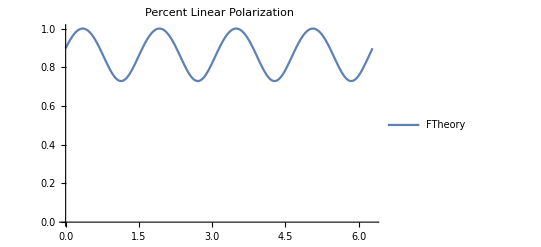

```mathematica
retardance=3.38;
shift795=42*π/180;
shift633=-20*π/180;
shift=shift633;
theory=Plot[Legended[Sqrt[(((LR[θ+shift,retardance].newLP.inc)[[2]])^2+((LR[θ+shift,retardance].newLP.inc)[[3]])^2)]/(LR[θ+shift,retardance].newLP.inc)[[1]],"FTheory"],{θ,0,2π},PlotRange->{0,Automatic},PlotLabel->"Percent Linear Polarization"]
```

```mathematica
Rasterize[Show[plot795,theory]]
```

-Graphics-

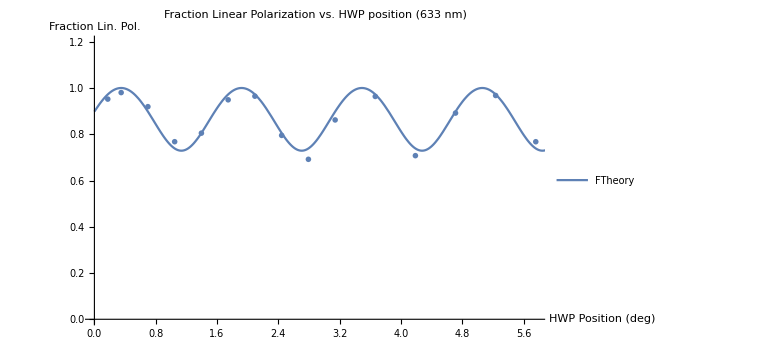

-Graphics-

```mathematica
Show[plot633,theory]
Rasterize[%]
```

1.5708

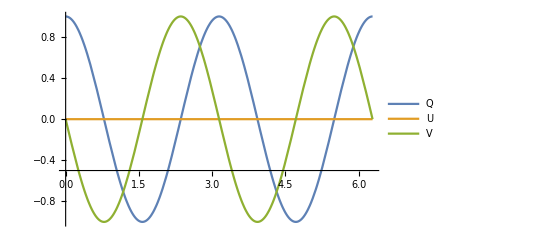

3.14159

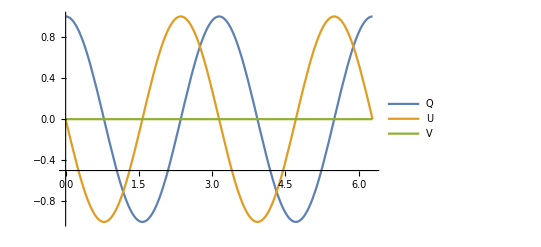

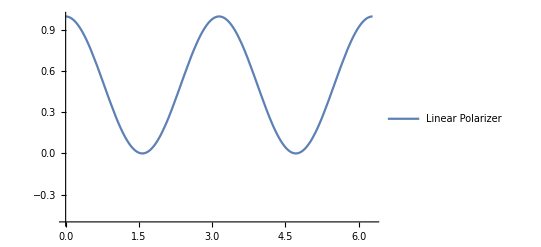

```mathematica
retard=.25*2*π
Plot[{Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[2]],"Q"],Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[3]],"U"],Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[4]],"V"]},{θ,0,2π},AxesOrigin->{0,-.5}]
retard=.5*2*π
Plot[{Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[2]],"Q"],Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[3]],"U"],Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[4]],"V"]},{θ,0,2π},AxesOrigin->{0,-.5}]
Plot[Legended[(LPzero.MuellerRotation[θ].inc)[[2]],"Linear Polarizer"],{θ,0,2π},AxesOrigin->{0,-.5}]
```